# done

### colors

```mathematica
$dkgreen = RGBColor["#242"]; (* header *)
$ltgreen = RGBColor["#464"]; (* h4 *)
$ltgreen = RGBColor["#686"]; (* h5 *)
$btgreen = RGBColor["#bdb"]; (* hr *)
$pgray = RGBColor["#888"]; (* p *)
$dpgray = RGBColor["#222"]; (* .dp *)
$lavender = RGBColor["#e6e6fa"]; (* footer *)
$mdlav = RGBColor["#c8c"]; (* link hover *)
$btlav = RGBColor["#dbd"]; (* button *)

systemColorsUsed = {Purple, LightPurple, Magenta, Gray};
```

```mathematica
Join[
ToExpression[Cases[Names["Global`*"], s_String /; MatchQ[StringTake[s, 1], "$"]]],
systemColorsUsed
]
```

{RGBColor[0.7333333333333333, 0.8666666666666667, 0.7333333333333333],RGBColor[0.8666666666666667, 0.7333333333333333, 0.8666666666666667],RGBColor[0.13333333333333333, 0.26666666666666666, 0.13333333333333333],RGBColor[0.13333333333333333, 0.13333333333333333, 0.13333333333333333],RGBColor[0.9019607843137255, 0.9019607843137255, 0.9803921568627451],RGBColor[0.4, 0.5333333333333333, 0.4],RGBColor[0.8, 0.5333333333333333, 0.8],RGBColor[0.5333333333333333, 0.5333333333333333, 0.5333333333333333],RGBColor[0.5, 0, 0.5],RGBColor[0.94, 0.88, 0.94],RGBColor[1, 0, 1],GrayLevel[0.5]}

## icon.ico

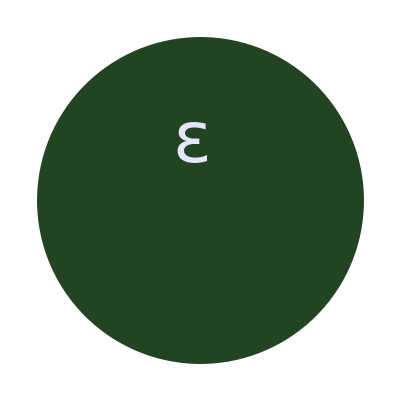

```mathematica
Graphics[{
$dkgreen,Disk[],$lavender, Inset[Style["ε", 750], {-0.05,0.35}]
}, Background->None, PlotRangePadding->0, PlotRange-> {{-1,1}, {-1, 1}}]
Export["/Users/annemarietorresen/Git/epsilon/images/icon.ico", %, Background -> None]
```

## epsilon-delta-plot.png

```mathematica
f[x_]:= 0.178211 E^(1.21145 x);
left = 0;
bot = 0.15;
```

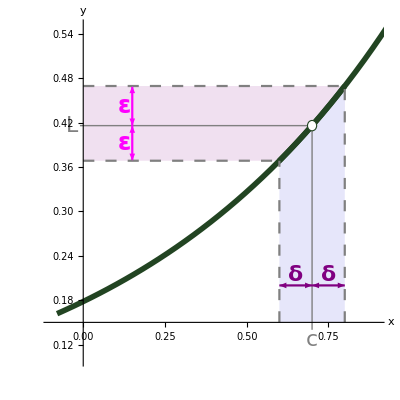

/Users/annemarietorresen/Desktop/epsilon/images/epsilon-delta-plot.png

```mathematica
Plot[{f[x], Piecewise[{{f[x],0.6<x<0.8}, {Undefined, True},{Interval[{0,1}],1/2<=x<=1}}]}, {x, -0.08, 1.2},
Ticks->None,
AxesLabel-> {Style["x", Italic], Style["y", Italic]},
LabelStyle->18,
AspectRatio->1,
AxesOrigin->{left,bot},
PlotStyle -> {{Thickness[0.01], $dkgreen}},
FillingStyle->$lavender,
Background-> None,
PlotRange-> {{-0.1, 0.9}, {0.1, 0.55}},
Filling -> {2->bot},
Prolog->{LightPurple, Rectangle[{0, f[0.6]}, {0.8, f[0.8]}]},
Epilog->{
Gray,
Line[{{0.7,bot-0.01},{0.7, f[0.7]} }], Inset["c", {0.7,bot-0.01}, Top],
Line[{{left-0.01,f[0.7]},{0.7, f[0.7]} }], Inset["L", {left-0.015,f[0.7]}, Right],
Thickness[0.004],
Purple,
Arrowheads[{-0.03, 0.03}],
Arrow[{{0.6, 0.2}, {0.7, 0.2}}], Arrow[{{0.8, 0.2}, {0.7, 0.2}}],
Inset["δ", {0.65, 0.2}, Bottom], Inset["δ", {0.75, 0.2}, Bottom],
Magenta,
Arrow[{{0.15, f[0.6]}, {0.15, f[0.7]}}], Arrow[{{0.15, f[0.8]}, {0.15, f[0.7]}}],
Inset["ε", {0.125, f[0.7] -( f[0.7]- f[0.6])/2}], Inset["ε", {0.125, f[0.7] +( f[0.8]- f[0.7])/2}],
Dashing[0.02], Gray,
Line[{{0.6,bot},{0.6, f[0.6]} }],Line[{{0.8,bot},{0.8, f[0.8]} }],
Line[{{0, f[0.6]},{0.6, f[0.6]} }],Line[{{0,f[0.8]},{0.8, f[0.8]} }],
Dashing[1],
FaceForm[White],EdgeForm[Directive[Thick, $dkgreen]], Ellipsoid[{0.7, f[0.7]}, {0.014,0.007}]
} 
]/. Inset[s_, r__] :> Inset[Style[s, If[MatchQ[s, ("L"|"c")], Italic, Bold], FontSize -> If[s == "ε", 24, 22], FontFamily->"Menlo"], r]
Export["/Users/annemarietorresen/Git/epsilon/images/epsilon-delta-plot.png", %, Background -> None]
```

# working

## upstream infographics - TODO

90% of a product’s environmental impact happens before you even open the package (https://zerowaste.org/)

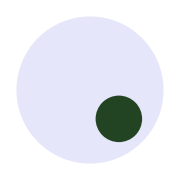

```mathematica
Graphics[{$lavender, (* area 10 *) Disk[{0,0}, Sqrt[10/Pi]], $dkgreen,(* area 10% of 10 *) Disk[{0.7, -0.7}, Sqrt[1/Pi]]}, ImageSize -> Small]
```

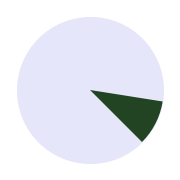

```mathematica
Graphics[{$lavender, (* 100% *) Disk[{0,0}, 1], $dkgreen,(* 10% *) Disk[{0,0}, 1, {0, 2Pi/10} - Pi/4]}, ImageSize -> Small]
```

World Resources Institute, and World Business Council for Sustainable Development. “Corporate Value Chain (Scope 3) Accounting and Reporting Standard: Supplement to the GHG Protocol Corporate Accounting and Reporting Standard .” Retrieved from https://www.epa.gov/climateleadership/scope-3-inventory-guidance on 29 Apr 2025.